# Shubham Kumar

## Simulate Audio for Conversations with Different Arrangements of Speakers.

## Project Timeline

### Project steps so far

#### Using distance from speaker (sound source) to each ear as the only parameter to determine delay amplitude of sound to send to each ear [Wednesday, Thursday]

Calculating distance to each ear and dividing by speed of sound to determine the delay, implemented simple attenuation to account for signal reduction.

```mathematica
Point2dAudioV1[file_, speakerPoint_, leftEar_, rightEar_, amplificationProportion_, trimStart_, trimEnd_]:=
Module[{fileLoc=file, speakerPointLoc=speakerPoint, leftEarPointLoc=leftEar, rightEarPointLoc=rightEar, k=amplificationProportion, t1=trimStart, t2=trimEnd},
(*Trimming Raw Audio & Separating Audio for each Channel*)
rawAudioData = Import[fileLoc];
trimmedRawAudioData = AudioNormalize[AudioTrim[rawAudioData,{t1, t2}]];
leftAudioData = AudioPan[trimmedRawAudioData,-1.];
rightAudioData = AudioPan[trimmedRawAudioData, 1.];

(*Calculating Delays*)
leftEarDistanceFromSpeaker = Quantity[√((leftEarPointLoc[[1]]-speakerPointLoc[[1]])^2.+(leftEarPointLoc[[2]]-speakerPointLoc[[2]])^2.), "centimeters"];
rightEarDistanceFromSpeaker = Quantity[√((rightEarPointLoc[[1]]-speakerPointLoc[[1]])^2.+(rightEarPointLoc[[2]]-speakerPointLoc[[2]])^2.), "centimeters"];
speedOfSound = StandardAtmosphereData[Quantity[0, "feet"],"SoundSpeed"];
leftEarAudioDelay = leftEarDistanceFromSpeaker/speedOfSound;
rightEarAudioDelay = rightEarDistanceFromSpeaker/speedOfSound;

(*Debug*)
Print["Left Ear Audio Distance:"]; Print[leftEarDistanceFromSpeaker];
Print["Right Ear Audio Distance:"]; Print[rightEarDistanceFromSpeaker];
Print["Left Ear Audio Delay:"]; Print[leftEarAudioDelay];
Print["Right Ear Audio Delay:"]; Print[rightEarAudioDelay];

(*Audio Delaying & Trash Attenuation*)
leftEarAudioDelayedData = If[QuantityMagnitude[leftEarDistanceFromSpeaker] ≠ 0, 
AudioAmplify[AudioDelay[leftAudioData, leftEarAudioDelay], QuantityMagnitude[k/leftEarDistanceFromSpeaker]], 
leftAudioData];
rightEarAudioDelayedData = If[QuantityMagnitude[rightEarDistanceFromSpeaker]≠ 0, 
AudioAmplify[AudioDelay[rightAudioData, rightEarAudioDelay], QuantityMagnitude[k/rightEarDistanceFromSpeaker]], 
rightAudioData];

(*Audio Delaying & Less Trash Attenuation - Needs to be completed*)

(*Mixing to Generate Final Sound*)
AudioNormalize[AudioChannelCombine[{leftEarAudioDelayedData, rightEarAudioDelayedData}]]
]
```

```mathematica
delayTest = Point2dAudioV1["/Users/shubhamkumar/Downloads/prenks/Thunder - LDR.mp3",{0,0},{-60,200},{-82,200}, 150, 0, 30]
```

Left Ear Audio Distance:

208.806 cm

Right Ear Audio Distance:

216.157 cm

Left Ear Audio Delay:

0.00613612 s

Right Ear Audio Delay:

0.00635215 s

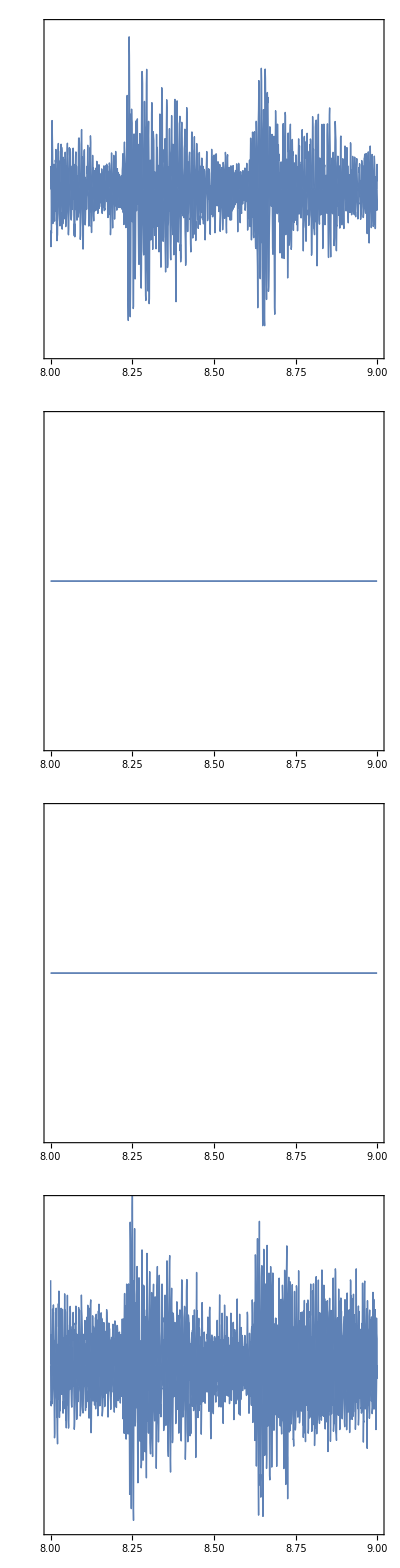

```mathematica
AudioPlot[delayTest, PlotRange->{{8,9},{-0.8, 0.8}}]
```

What were the shortcomings with this approach?

Attenuation wasn’t implemented well, ISQ -6dB observation was difficult to incorporate in the function.

Including the user’s head as an obstacle accurately seemed to be next to impossible with my knowledge.

Attenuation with Doppler’s effect was computationally inefficient and led to rough audio.

I don’t have enough knowledge in mathematics to implement my own versions of solutions to combat the problems stated above. Adding in things like Impedance Boundaries & dB (SPL) monitoring would be quite difficult. Fortunately, there are tutorials on Wolfram Documentation dedicated to explaining the field of acoustics and how sound propagation can be modeled.

#### Familiarizing myself with basic physics terminology in Acoustics. [Friday]

Used the following resources.

Yi-Lin Chiu’s talk about modeling acoustics with PDEs.

Frequency vs Time Domain Modeling, Articles on Wolfram.

Additional information about dB, Sound Pressure, Sound Energy, Sound Intensity (etc) from sites like Wikipedia.

```mathematica
Implementing my own Wave PDE to model sound propagation in a region [Saturday, Sunday]
```

### Future step(s)

Modifying boundary conditions for obstacles and walls to be impedance boundaries.

Figure out how to change radiation boundary to output an audio object instead of a monotone frequency.

Improve curve fitting, possibly using Fourier Transform to generate the audio object after collecting data from the Wave PDE.

Understand how to add motion to the Wave PDE.

Understand Time vs Frequency Domains.

## Using Acoustics to Model a Region using the Wave PDE in the Time Domain

Most recently I’ve been working on using the wave PDE and boundary conditions to simulate sound propagation in a region.

Defining a Region

```mathematica
OΩ = RegionDifference[RegionDifference[Rectangle[{0,0},{0.25,0.25}],Disk[{0.1,0.1}, 0.025]],Disk[{0.25,0},0.0125]];
```

Plotting to Visualize

```mathematica
RegionPlot[OΩ,Sequence[AspectRatio->1,ImageSize->Medium], PlotStyle->"Scientific"]
```

-Graphics-

Setting Boundary Conditions [Issue] Setting Impedance Boundary Condition? Radiating Complex Signals instead of Monotone Frequencies.

```mathematica
Gabc = NeumannValue[-((I ω)/(ρ c))*p[x,y],y≥0.0125&&x≤ 0.2375];
Grbc = NeumannValue[-((I ω)/(ρ c))*p[x,y]+(2 I ω)/(ρ c)*5,{x,y} ∈Disk[{0.25,0},0.012501]];
```

Setting Sound and Air Attributes

```mathematica
Cair=QuantityMagnitude[ThermodynamicData["Air","SoundSpeed"]];
Pair=QuantityMagnitude[ThermodynamicData["Air","Density"]];
```

```mathematica
Oλ=1/10;
Of=Cair/Oλ;
```

Defining the PDE

```mathematica
Opde={-((ω^2 p[x,y])/(c^2 ρ))+Inactive[Div][({{-(1/ρ),0},{0,-(1/ρ)}}.Inactive[Grad][p[x,y],{x,y}]),{x,y}]==Gabc+Grbc}/.{c->Cair,ρ->Pair,ω->2 π Of};
```

Solving the PDE

```mathematica
pfun=NDSolveValue[Opde,p,{x,y}∈OΩ,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->1/40000}}}]
```

InterpolatingFunction[…]

Visualizing Change in Pressure in the Region Over Time in 2D

```mathematica
(*frames=Table[ContourPlot[Re[pfun[x,y]*Exp[I ω t]/.{ω->2 π Of}],{x,y}∈OΩ,Sequence[PlotRange->{-7.5,7.5},ColorFunction->ColorData[{"SunsetColors",{-3,3}}],ColorFunctionScaling->False,Contours->Apply[Range,Flatten[{{-3,3},(1/8) Abs[Apply[Subtract,{-3,3}]]}]],PlotPoints->41,AspectRatio->Automatic,PlotLegends->Automatic]],{t,0,0.001,0.001/25}];ListAnimate[frames]*)
```

```mathematica
Import["/Users/shubhamkumar/Desktop/oren5.gif","Animation"]
```

Visualizing Change in Pressure in the Region Over Time in 3D

```mathematica
(*frames3d = Animate[Plot3D[Re[pfun[x,y]*Exp[I ω 0.001t]/.{ω->2 π Of}], {x,0,0.25}, {y,0,0.25},PlotRange->{{0,0.25},{0,0.25},{-5,5}},PerformanceGoal->"Quality",ViewPoint->{Pi,2Pi*t,2}],{t,0,1}]*)
```

Output GIF Animation

```mathematica
Import["/Users/shubhamkumar/Desktop/oren4.gif","Animation"]
```

## Extracting Sound Pressure Data for Left Ear & Right Ear

Using PDE to Extract SPL for each Ear

```mathematica
leftEar ={#, Re[pfun[0.075,0.1]*Exp[I ω #]/.{ω->2 π Of}]}&/@Table[t, {t,0,0.001,0.001/100}];
rightEar ={ #,Re[pfun[0.125,0.1]*Exp[I ω #]/.{ω->2 π Of}]}&/@Table[t, {t,0,0.001,0.001/100}];
```

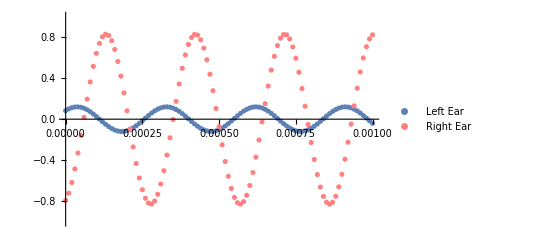

```mathematica
leftEarPlot = ListPlot[leftEar,PlotLegends->{"Left Ear"}, PlotRange->{{0,0.001}, {-1,1}}];
rightEarPlot = ListPlot[rightEar,PlotLegends->{"Right Ear"},PlotStyle->{Pink},PlotRange->{{0,0.001}, {-1,1}}];
Show[leftEarPlot,rightEarPlot]
```

Fitting a Model to the Data for each Ear [Issue] Fourier Transform to Fit a Model when Frequencies become Increasingly Complex?

```mathematica
fittedModelRightEar =NonlinearModelFit[rightEar,0.8274376082610522 Sin[b x+c],{{b,21600}, {c,4.95}},x, MaxIterations->Automatic, Method->NMinimize];
fittedModelLeftEar =NonlinearModelFit[leftEar,0.12012126831185457 Sin[b x+c],{{b,21400}, {c,0.88}},x, MaxIterations->Automatic, Method->NMinimize];
```

NonlinearModelFit::ivar: {{Country/Region,1/22/20,1/23/20,1/24/20,1/25/20,1/26/20,1/27/20,1/28/20,1/29/20,1/30/20,1/31/20,2/1/20,2/2/20,2/3/20,2/4/20,2/5/20,2/6/20,2/7/20,2/8/20,2/9/20,2/10/20,2/11/20,2/12/20,«5»,2/18/20,2/19/20,2/20/20,2/21/20,2/22/20,2/23/20,2/24/20,2/25/20,2/26/20,2/27/20,2/28/20,2/29/20,3/1/20,3/2/20,3/3/20,3/4/20,3/5/20,3/6/20,3/7/20,3/8/20,3/9/20,3/10/20,«124»},«49»,«132»} is not a valid variable.

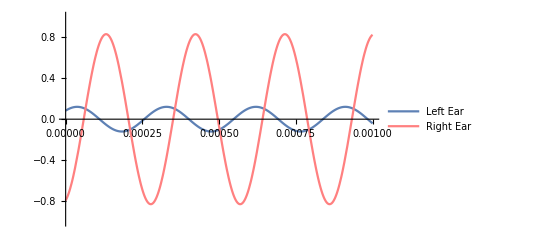

```mathematica
Show[
Plot[fittedModelLeftEar[x],{x,0,0.0010},PlotRange->{{0,0.001},{-1,1}},PlotLegends->{"Left Ear"}],Plot[fittedModelRightEar[x],{x,0,0.0010}, PlotRange->{{0,0.001},{-1,1}},PlotStyle->{Pink},PlotLegends->{"Right Ear"}]]
```

```mathematica
Normal/@{fittedModelRightEar, fittedModelLeftEar}
```

{0.827438 sin(21572.9 x+5.01114),0.120121 sin(21572.9 x+0.762724)}

Audio isn’t Particularly Interesting because the Radiation Boundary is Emitting a Single Frequency

```mathematica
leftEarAudioFreqPhase = AudioGenerator[{"Sin",21572.932190413565 /10,0.7627240470048269/10}];
rightEarAudioFreqPhase = AudioGenerator[{"Sin",21572.932516494737/10,5.0111372046811535/10}];
```

```mathematica
leftEarAudioMono = AudioPan[leftEarAudioFreqPhase, -1.];
rightEarAudioMono =AudioPan[rightEarAudioFreqPhase, 1.];
```

```mathematica
leftEarAudio = AudioAmplify[leftEarAudioMono,0.12012126831185457 ];
rightEarAudio = AudioAmplify[rightEarAudioMono,0.8274376082610522];
```

```mathematica
finalAudio =AudioChannelCombine[{leftEarAudio, rightEarAudio}]
```

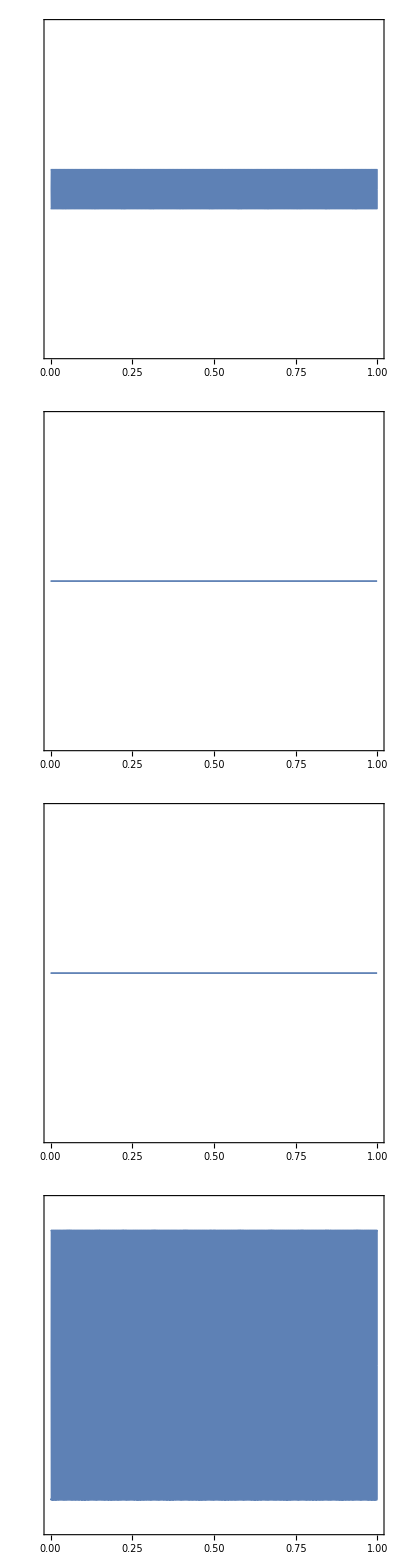

-Graphics-

```mathematica
AudioPlot[finalAudio]
Spectrogram[finalAudio]
```

## Issues & Questions

### Issues

```mathematica
NotebookLocate["Issue"]
```

### Questions

Time vs. Frequency Domain? Would I need to model both? - Spoke with Carlo, need to only model Frequency Domain & Map the Attenuation Coefficient.

Better way to assign boundary conditions? - setting inequalities manually is tedious.

Is there a way to adjust the radiating boundary so it emits more complex signals? - Using Frequency Domain Now.

Better fit models for complex signals when sampled from acoustic model? - Will be using FFT.